### Start choosing the example:

```mathematica
t=20;
beta = 1;
A =0;
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/D2E2.m"];
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U1},{8,U2},{9,U3}},"Switching Costs"->{{5,6,7,1},{5,6,8,1},{5,6,9,1},{7,6,5,1},{7,6,8,1},{7,6,9,1},{8,6,5,1},{8,6,7,1},{8,6,9,1},{9,6,5,1},{9,6,7,1},{9,6,8,1}}|>;
CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}]]//AbsoluteTiming
(*MFGPreprocessing[d2e];*)
```

tripleclean done!

Preprocessing done!

{0.225708,<|j24→1,j26→2,j23→0,j25→0,j17→0,j19→0,j21→0,j2→1,j4→2,j1→0,j3→0,j6→3,j5→0,j8→3,j7→0,j10→3,j9→0,j12→2,j14→1,j16→0,j11→0,j18→2,j13→0,j20→1,j15→0,j22→0,u18→1,u20→2,u22→3,jt1→0,jt11→3,jt13→3,jt14→0,jt17→0,jt2→1,jt20→0,jt23→0,jt24→0,jt26→0,jt27→2,jt28→0,jt29→1,jt3→0,jt30→0,jt31→0,jt32→0,jt4→2,jt5→0,jt6→1,jt7→0,jt8→2,jt9→0,u12→1,u14→2,u16→3,u17→1,u19→2,u2→13,u21→3,u23→14,u24→14,u25→15,u3→15,u5→13,u7→10,u9→7,jt10→0,jt12→0,jt18→0,jt19→0,jt21→0,jt22→0,jt25→0,u1→14,u11→3,u13→3,u15→3,u26→15,u4→13,u6→10,u8→7,jt15→2,jt16→1,u10→4|>}

```mathematica
MFGEquations=D2E[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}];//Timing
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

{0.257057,Null}

```mathematica
Keys@MFGEquations
```

{Vertices List,Adjacency Matrix,Entrance Vertices and Currents,Exit Vertices and Terminal Costs,Switching Costs,BG,InEdges,OutEdges,FG,jvars,jtvars,uvars,jays,AllOr,AllIneq,EqPosJs,EqCurrentCompCon,EqTransitionCompCon,EqAllAll,BoundaryRules,InitRules,RulesCriticalCase,RuleEntryIn,Nlhs,MinimalTimeRhs,EqCriticalCase,EqSwitchingConditions,Nrhs}

```mathematica
MFGEquations["RulesCriticalCase"]
```

<|j2→1,j23→0,j4→2,j25→0,j1→0,j3→0,j6→jt13,j5→-3+jt13,j8→jt13,j7→-3+jt13,j10→jt13,j9→-3+jt13,j12→jt15-jt21-jt23+jt25,j14→3-jt15-jt17-jt20+jt21-jt25,j16→jt17+jt20+jt23,j11→0,j18→jt15-jt21-jt23+jt25,j13→0,j20→3-jt15-jt17-jt20+jt21-jt25,j15→0,j22→jt17+jt20+jt23,j24→1,j26→2,u18→1,u20→2,u22→3,u4→-1+u1,u5→-1+u1,u7→-4+u1,u9→-7+u1,u11→-10+u1,u13→-10+u1,u15→-10+u1,jt1→0,jt28→0,jt3→0,jt30→0,jt32→0,u17→1,u19→2,u21→3,u24→u23,u26→u25,j17→0,j19→0,j21→0,jt10→-1+jt6,jt11→jt13,jt12→-3+jt13,jt14→-3+jt13,jt16→jt13-jt15-jt17,jt19→-jt18-jt20,jt2→1,jt22→-jt21-jt23,jt24→-3+jt13-jt18-jt21,jt26→3-jt13+jt18+jt21-jt25,jt27→jt15-jt21-jt23+jt25,jt29→3-jt15-jt17-jt20+jt21-jt25,jt31→jt17+jt20+jt23,jt4→2,jt5→1-jt6,jt7→2-jt13+jt6,jt8→jt13-jt6,jt9→-2+jt13-jt6,u10→-10+u1,u12→-10-jt15+jt21+jt23-jt25+u1,u14→-13+jt15+jt17+jt20-jt21+jt25+u1,u16→-10-jt17-jt20-jt23+u1,u2→-1+u1,u3→1+u1,u6→-4+u1,u8→-7+u1|>

```mathematica
MFGEquations["EqCriticalCase"]//Solve
```

{{u12→j11-j12+u11,u14→j13-j14+u13,u16→j15-j16+u15,u2→j1-j2+u1,u4→j3-j4+u3,u6→j5-j6+u5,u8→j7-j8+u7,u9→j10-j9+u10}}

```mathematica
Values@MFGEquations["uvars"]/.MFGEquations["InitRules"]
```

{u1,u2,u3,u2,u2,u6,u6,u8,u8,u10,u10,u12,u10,u14,u10,u16,1,1,2,2,3,3,u23,u23,u25,u25}

```mathematica
MFGEquations["EqCriticalCase"]/.MFGEquations["InitRules"]
```

1-u1+u2==0&&2+u2-u3==0&&3-u2+u6==0&&3-u6+u8==0&&3+u10-u8==0&&jt15-jt21-jt23+jt25-u10+u12==0&&3-jt15-jt17-jt20+jt21-jt25-u10+u14==0&&jt17+jt20+jt23-u10+u16==0

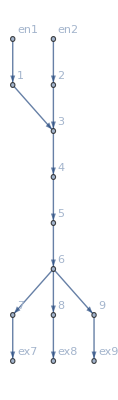

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

```mathematica
oldrules=<|j641->1,j642->2,j643->3,j644->3,j645->3,j646->2,j647->1,j648->0,j649->2,j650->1,j651->0,j652->1,j653->2,j654->0,j655->0,j656->0,j657->0,j658->0,j659->0,j660->0,j661->0,j662->0,j663->0,j664->0,j665->0,j666->0,jt667->0,jt668->1,jt669->0,jt670->2,jt671->0,jt672->1,jt673->0,jt674->2,jt675->0,jt676->0,jt677->3,jt678->0,jt679->3,jt680->0,jt681->2,jt682->1,jt683->0,jt684->0,jt685->0,jt686->0,jt687->0,jt688->0,jt689->0,jt690->0,jt691->0,jt692->0,jt693->2,jt694->0,jt695->1,jt696->0,jt697->0,jt698->0,u699->13,u700->14,u701->12,u702->9,u703->6,u704->3,u705->3,u706->3,u707->1,u708->2,u709->3,u710->13,u711->14,u712->12,u713->12,u714->9,u715->6,u716->3,u717->1,u718->2,u719->3,u720->1,u721->2,u722->3,u723->13,u724->14|>;
```

{<|u1→13,u2→12,u3→14,u4→12,u5→12,u6→9,u7→9,u8→6,u9→6,u10→3,u11→3,u12→1,u13→3,u14→2,u15→3,u16→3,u17→1,u18→1,u19→2,u20→2,u21→3,u22→3,u23→13,u24→13,u25→14,u26→14,j1→0,j2→1,j3→0,j4→2,j5→0,j6→3,j7→0,j8→3,j9→0,j10→3,j11→0,j12→2,j13→0,j14→1,j15→0,j16→0,j17→0,j18→2,j19→0,j20→1,j21→0,j22→0,j23→0,j24→1,j25→0,j26→2|>}

```mathematica
(rul=CriticalCongestionSolver2[MFGEquations];)//AbsoluteTiming
```

EliminateVarsSimplify for the us

Finished with the us!

Finish with the js

{0.068707,Null}

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==-0.259921&&j642-j655-u700+u713==0.412599&&j643-j656-u701+u714==1.18288&&j644-j657-u702+u715==1.18288&&j645-j658-u703+u716==1.18288&&j646-j659-u704+u717==0.412599&&j647-j660-u705+u718==-0.259921&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.136349

FRX1: nonlinear: 
j641-j654-u699+u712==-0.259921&&j642-j655-u700+u713==0.412599&&j643-j656-u701+u714==1.18288&&j644-j657-u702+u715==1.18288&&j645-j658-u703+u716==1.18288&&j646-j659-u704+u717==0.664462&&j647-j660-u705+u718==-0.435289&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0786988

FRX1: nonlinear: 
j641-j654-u699+u712==-0.259921&&j642-j655-u700+u713==0.412599&&j643-j656-u701+u714==1.18288&&j644-j657-u702+u715==1.18288&&j645-j658-u703+u716==1.18288&&j646-j659-u704+u717==0.828603&&j647-j660-u705+u718==-0.515454&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0416684

FRX1: nonlinear: 
j641-j654-u699+u712==-0.259921&&j642-j655-u700+u713==0.412599&&j643-j656-u701+u714==1.18288&&j644-j657-u702+u715==1.18288&&j645-j658-u703+u716==1.18288&&j646-j659-u704+u717==0.923697&&j647-j660-u705+u718==-0.5409&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0198755

FRX1: nonlinear: 
j641-j654-u699+u712==-0.259921&&j642-j655-u700+u713==0.412599&&j643-j656-u701+u714==1.18288&&j644-j657-u702+u715==1.18288&&j645-j658-u703+u716==1.18288&&j646-j659-u704+u717==0.97092&&j647-j660-u705+u718==-0.544306&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00833631

FRX1: nonlinear: 
j641-j654-u699+u712==-0.259921&&j642-j655-u700+u713==0.412599&&j643-j656-u701+u714==1.18288&&j644-j657-u702+u715==1.18288&&j645-j658-u703+u716==1.18288&&j646-j659-u704+u717==0.990812&&j647-j660-u705+u718==-0.543174&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00310576

FRX1: nonlinear: 
j641-j654-u699+u712==-0.259921&&j642-j655-u700+u713==0.412599&&j643-j656-u701+u714==1.18288&&j644-j657-u702+u715==1.18288&&j645-j658-u703+u716==1.18288&&j646-j659-u704+u717==0.99819&&j647-j660-u705+u718==-0.542287&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0010783

FRX1: nonlinear: 
j641-j654-u699+u712==-0.259921&&j642-j655-u700+u713==0.412599&&j643-j656-u701+u714==1.18288&&j644-j657-u702+u715==1.18288&&j645-j658-u703+u716==1.18288&&j646-j659-u704+u717==1.00074&&j647-j660-u705+u718==-0.541916&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000363157

FRX1: nonlinear: 
j641-j654-u699+u712==-0.259921&&j642-j655-u700+u713==0.412599&&j643-j656-u701+u714==1.18288&&j644-j657-u702+u715==1.18288&&j645-j658-u703+u716==1.18288&&j646-j659-u704+u717==1.0016&&j647-j660-u705+u718==-0.541783&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00012095

FRX1: nonlinear: 
j641-j654-u699+u712==-0.259921&&j642-j655-u700+u713==0.412599&&j643-j656-u701+u714==1.18288&&j644-j657-u702+u715==1.18288&&j645-j658-u703+u716==1.18288&&j646-j659-u704+u717==1.00189&&j647-j660-u705+u718==-0.541738&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000040129

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.77181,j647→0.228186,j648→2.77556×10^-17,j649→2.77181,j650→0.228186,j651→2.77556×10^-17,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.77181,jt682→0.228186,jt683→2.77556×10^-17,jt684→0,jt685→0,jt686→0,jt687→0,jt688→2.77556×10^-17,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.77181,jt694→0,jt695→0.228186,jt696→0,jt697→2.77556×10^-17,jt698→0,u699→9.48121,u700→9.80869,u701→8.22129,u702→6.40417,u703→4.58704,u704→2.76992,u705→2.76992,u706→2.76992,u707→1,u708→2,u709→3,u710→9.48121,u711→9.80869,u712→8.22129,u713→8.22129,u714→6.40417,u715→4.58704,u716→2.76992,u717→1.,u718→2.,u719→2.76992,u720→1,u721→2,u722→3,u723→9.48121,u724→9.80869|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==-0.240004&&j642-j655-u700+u713==0.387102&&j643-j656-u701+u714==1.11895&&j644-j657-u702+u715==1.11895&&j645-j658-u703+u716==1.11895&&j646-j659-u704+u717==0.387102&&j647-j660-u705+u718==-0.240004&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.126125

FRX1: nonlinear: 
j641-j654-u699+u712==-0.240004&&j642-j655-u700+u713==0.387102&&j643-j656-u701+u714==1.11895&&j644-j657-u702+u715==1.11895&&j645-j658-u703+u716==1.11895&&j646-j659-u704+u717==0.609049&&j647-j660-u705+u718==-0.388647&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0687182

FRX1: nonlinear: 
j641-j654-u699+u712==-0.240004&&j642-j655-u700+u713==0.387102&&j643-j656-u701+u714==1.11895&&j644-j657-u702+u715==1.11895&&j645-j658-u703+u716==1.11895&&j646-j659-u704+u717==0.743796&&j647-j660-u705+u718==-0.453002&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0348351

FRX1: nonlinear: 
j641-j654-u699+u712==-0.240004&&j642-j655-u700+u713==0.387102&&j643-j656-u701+u714==1.11895&&j644-j657-u702+u715==1.11895&&j645-j658-u703+u716==1.11895&&j646-j659-u704+u717==0.817147&&j647-j660-u705+u718==-0.475679&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0163218

FRX1: nonlinear: 
j641-j654-u699+u712==-0.240004&&j642-j655-u700+u713==0.387102&&j643-j656-u701+u714==1.11895&&j644-j657-u702+u715==1.11895&&j645-j658-u703+u716==1.11895&&j646-j659-u704+u717==0.852747&&j647-j660-u705+u718==-0.48233&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00710568

FRX1: nonlinear: 
j641-j654-u699+u712==-0.240004&&j642-j655-u700+u713==0.387102&&j643-j656-u701+u714==1.11895&&j644-j657-u702+u715==1.11895&&j645-j658-u703+u716==1.11895&&j646-j659-u704+u717==0.868455&&j647-j660-u705+u718==-0.484148&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00293767

FRX1: nonlinear: 
j641-j654-u699+u712==-0.240004&&j642-j655-u700+u713==0.387102&&j643-j656-u701+u714==1.11895&&j644-j657-u702+u715==1.11895&&j645-j658-u703+u716==1.11895&&j646-j659-u704+u717==0.874979&&j647-j660-u705+u718==-0.484679&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00118117

FRX1: nonlinear: 
j641-j654-u699+u712==-0.240004&&j642-j655-u700+u713==0.387102&&j643-j656-u701+u714==1.11895&&j644-j657-u702+u715==1.11895&&j645-j658-u703+u716==1.11895&&j646-j659-u704+u717==0.877606&&j647-j660-u705+u718==-0.484854&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000468935

FRX1: nonlinear: 
j641-j654-u699+u712==-0.240004&&j642-j655-u700+u713==0.387102&&j643-j656-u701+u714==1.11895&&j644-j657-u702+u715==1.11895&&j645-j658-u703+u716==1.11895&&j646-j659-u704+u717==0.87865&&j647-j660-u705+u718==-0.484917&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000185186

FRX1: nonlinear: 
j641-j654-u699+u712==-0.240004&&j642-j655-u700+u713==0.387102&&j643-j656-u701+u714==1.11895&&j644-j657-u702+u715==1.11895&&j645-j658-u703+u716==1.11895&&j646-j659-u704+u717==0.879062&&j647-j660-u705+u718==-0.484941&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000729752

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.682,j647→0.317999,j648→1.66533×10^-16,j649→2.682,j650→0.317999,j651→1.66533×10^-16,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.682,jt682→0.317999,jt683→1.66533×10^-16,jt684→0,jt685→0,jt686→0,jt687→0,jt688→1.66533×10^-16,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.682,jt694→0,jt695→0.317999,jt696→0,jt697→1.66533×10^-16,jt698→0,u699→9.68609,u700→10.059,u701→8.44609,u702→6.56504,u703→4.68399,u704→2.80294,u705→2.80294,u706→2.80294,u707→1,u708→2,u709→3,u710→9.68609,u711→10.059,u712→8.44609,u713→8.44609,u714→6.56504,u715→4.68399,u716→2.80294,u717→1.,u718→2.,u719→2.80294,u720→1,u721→2,u722→3,u723→9.68609,u724→10.059|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.328966&&j647-j660-u705+u718==-0.196864&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.104109

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.489498&&j647-j660-u705+u718==-0.296288&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0487977

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.57114&&j647-j660-u705+u718==-0.334113&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0217679

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.609118&&j647-j660-u705+u718==-0.34806&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0093318

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.62571&&j647-j660-u705+u718==-0.353316&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00390353

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.632707&&j647-j660-u705+u718==-0.355367&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00161274

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.635607&&j647-j660-u705+u718==-0.356188&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000662592

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.6368&&j647-j660-u705+u718==-0.356521&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000271577

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.63729&&j647-j660-u705+u718==-0.356656&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000111201

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.63749&&j647-j660-u705+u718==-0.356712&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000455142

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.637572&&j647-j660-u705+u718==-0.356734&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000186257

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.637606&&j647-j660-u705+u718==-0.356744&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.62163×10^-6

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.637619&&j647-j660-u705+u718==-0.356748&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.11868×10^-6

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.637625&&j647-j660-u705+u718==-0.356749&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.27611×10^-6

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.637627&&j647-j660-u705+u718==-0.35675&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.22163×10^-7

FRX1: nonlinear: 
j641-j654-u699+u712==-0.196864&&j642-j655-u700+u713==0.328966&&j643-j656-u701+u714==0.96872&&j644-j657-u702+u715==0.96872&&j645-j658-u703+u716==0.96872&&j646-j659-u704+u717==0.637628&&j647-j660-u705+u718==-0.35675&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.13659×10^-7

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.49719,j647→0.502811,j648→-2.22045×10^-16,j649→2.49719,j650→0.502811,j651→-2.22045×10^-16,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.49719,jt682→0.502811,jt683→-2.22045×10^-16,jt684→0,jt685→0,jt686→0,jt687→0,jt688→0.,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.49719,jt694→0,jt695→0.502811,jt696→0,jt697→-2.22045×10^-16,jt698→0,u699→10.1503,u700→10.6244,u701→8.9534,u702→6.92212,u703→4.89084,u704→2.85956,u705→2.85956,u706→2.85956,u707→1,u708→2,u709→3,u710→10.1503,u711→10.6244,u712→8.9534,u713→8.9534,u714→6.92212,u715→4.89084,u716→2.85956,u717→1.,u718→2.,u719→2.85956,u720→1,u721→2,u722→3,u723→10.1503,u724→10.6244|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==-0.0335578&&j642-j655-u700+u713==0.0649364&&j643-j656-u701+u714==0.207354&&j644-j657-u702+u715==0.207354&&j645-j658-u703+u716==0.207354&&j646-j659-u704+u717==0.0649364&&j647-j660-u705+u718==-0.0335578&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00691346

FRX1: nonlinear: 
j641-j654-u699+u712==-0.0335578&&j642-j655-u700+u713==0.0649364&&j643-j656-u701+u714==0.207354&&j644-j657-u702+u715==0.207354&&j645-j658-u703+u716==0.207354&&j646-j659-u704+u717==0.0711234&&j647-j660-u705+u718==-0.0366428&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000650351

FRX1: nonlinear: 
j641-j654-u699+u712==-0.0335578&&j642-j655-u700+u713==0.0649364&&j643-j656-u701+u714==0.207354&&j644-j657-u702+u715==0.207354&&j645-j658-u703+u716==0.207354&&j646-j659-u704+u717==0.071711&&j647-j660-u705+u718==-0.0369216&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000607656

FRX1: nonlinear: 
j641-j654-u699+u712==-0.0335578&&j642-j655-u700+u713==0.0649364&&j643-j656-u701+u714==0.207354&&j644-j657-u702+u715==0.207354&&j645-j658-u703+u716==0.207354&&j646-j659-u704+u717==0.0717659&&j647-j660-u705+u718==-0.0369476&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.67384×10^-6

FRX1: nonlinear: 
j641-j654-u699+u712==-0.0335578&&j642-j655-u700+u713==0.0649364&&j643-j656-u701+u714==0.207354&&j644-j657-u702+u715==0.207354&&j645-j658-u703+u716==0.207354&&j646-j659-u704+u717==0.071771&&j647-j660-u705+u718==-0.03695&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.29747×10^-7

FRX1: nonlinear: 
j641-j654-u699+u712==-0.0335578&&j642-j655-u700+u713==0.0649364&&j643-j656-u701+u714==0.207354&&j644-j657-u702+u715==0.207354&&j645-j658-u703+u716==0.207354&&j646-j659-u704+u717==0.0717715&&j647-j660-u705+u718==-0.0369502&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.94605×10^-8

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.05436,j647→0.945639,j648→1.11022×10^-16,j649→2.05436,j650→0.945639,j651→1.11022×10^-16,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.05436,jt682→0.945639,jt683→1.11022×10^-16,jt684→0,jt685→0,jt686→0,jt687→0,jt688→1.11022×10^-16,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.05436,jt694→0,jt695→0.945639,jt696→0,jt697→1.11022×10^-16,jt698→0,u699→12.3941,u700→13.2956,u701→11.3605,u702→8.56788,u703→5.77524,u704→2.98259,u705→2.98259,u706→2.98259,u707→1,u708→2,u709→3,u710→12.3941,u711→13.2956,u712→11.3605,u713→11.3605,u714→8.56788,u715→5.77524,u716→2.98259,u717→1.,u718→2.,u719→2.98259,u720→1,u721→2,u722→3,u723→12.3941,u724→13.2956|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==0&&j642-j655-u700+u713==0&&j643-j656-u701+u714==0&&j644-j657-u702+u715==0&&j645-j658-u703+u716==0&&j646-j659-u704+u717==0&&j647-j660-u705+u718==0&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[7.08458×10^-15,ComplexInfinity]

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2,j647→1,j648→0,j649→2,j650→1,j651→0,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2,jt682→1,jt683→0,jt684→0,jt685→0,jt686→0,jt687→0,jt688→0,jt689→0,jt690→0,jt691→0,jt692→0,jt693→2,jt694→0,jt695→1,jt696→0,jt697→0,jt698→0,u699→13,u700→14,u701→12,u702→9,u703→6,u704→3,u705→3,u706→3,u707→1,u708→2,u709→3,u710→13,u711→14,u712→12,u713→12,u714→9,u715→6,u716→3,u717→1,u718→2,u719→3,u720→1,u721→2,u722→3,u723→13,u724→14|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==0.311495&&j642-j655-u700+u713==-0.904846&&j643-j656-u701+u714==-3.74297&&j644-j657-u702+u715==-3.74297&&j645-j658-u703+u716==-3.74297&&j646-j659-u704+u717==-0.904846&&j647-j660-u705+u718==0.311495&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.169209

FRX1: nonlinear: 
j641-j654-u699+u712==0.311495&&j642-j655-u700+u713==-0.904846&&j643-j656-u701+u714==-3.74297&&j644-j657-u702+u715==-3.74297&&j645-j658-u703+u716==-3.74297&&j646-j659-u704+u717==0.119&&j647-j660-u705+u718==-0.109537&&j648-j661-u706+u719==0.174007

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.186459

FRX1: nonlinear: 
j641-j654-u699+u712==0.311495&&j642-j655-u700+u713==-0.904846&&j643-j656-u701+u714==-3.74297&&j644-j657-u702+u715==-3.74297&&j645-j658-u703+u716==-3.74297&&j646-j659-u704+u717==-1.02421&&j647-j660-u705+u718==0.362556&&j648-j661-u706+u719==0.105437

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.204291

FRX1: nonlinear: 
j641-j654-u699+u712==0.311495&&j642-j655-u700+u713==-0.904846&&j643-j656-u701+u714==-3.74297&&j644-j657-u702+u715==-3.74297&&j645-j658-u703+u716==-3.74297&&j646-j659-u704+u717==0.222099&&j647-j660-u705+u718==-0.158217&&j648-j661-u706+u719==0.23788

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.222908

FRX1: nonlinear: 
j641-j654-u699+u712==0.311495&&j642-j655-u700+u713==-0.904846&&j643-j656-u701+u714==-3.74297&&j644-j657-u702+u715==-3.74297&&j645-j658-u703+u716==-3.74297&&j646-j659-u704+u717==-1.16189&&j647-j660-u705+u718==0.371565&&j648-j661-u706+u719==0.126153

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.23509

FRX1: nonlinear: 
j641-j654-u699+u712==0.311495&&j642-j655-u700+u713==-0.904846&&j643-j656-u701+u714==-3.74297&&j644-j657-u702+u715==-3.74297&&j645-j658-u703+u716==-3.74297&&j646-j659-u704+u717==0.283182&&j647-j660-u705+u718==-0.217837&&j648-j661-u706+u719==0.270875

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.249585

FRX1: nonlinear: 
j641-j654-u699+u712==0.311495&&j642-j655-u700+u713==-0.904846&&j643-j656-u701+u714==-3.74297&&j644-j657-u702+u715==-3.74297&&j645-j658-u703+u716==-3.74297&&j646-j659-u704+u717==-1.27373&&j647-j660-u705+u718==0.370313&&j648-j661-u706+u719==0.143731

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.257286

FRX1: nonlinear: 
j641-j654-u699+u712==0.311495&&j642-j655-u700+u713==-0.904846&&j643-j656-u701+u714==-3.74297&&j644-j657-u702+u715==-3.74297&&j645-j658-u703+u716==-3.74297&&j646-j659-u704+u717==0.319986&&j647-j660-u705+u718==-0.260207&&j648-j661-u706+u719==0.29591

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.266054

FRX1: nonlinear: 
j641-j654-u699+u712==0.311495&&j642-j655-u700+u713==-0.904846&&j643-j656-u701+u714==-3.74297&&j644-j657-u702+u715==-3.74297&&j645-j658-u703+u716==-3.74297&&j646-j659-u704+u717==-1.34406&&j647-j660-u705+u718==0.365072&&j648-j661-u706+u719==0.15839

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.269878

FRX1: nonlinear: 
j641-j654-u699+u712==0.311495&&j642-j655-u700+u713==-0.904846&&j643-j656-u701+u714==-3.74297&&j644-j657-u702+u715==-3.74297&&j645-j658-u703+u716==-3.74297&&j646-j659-u704+u717==0.337998&&j647-j660-u705+u718==-0.281627&&j648-j661-u706+u719==0.31151

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.273849

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.21537,j647→0.595746,j648→0.188883,j649→2.21537,j650→0.595746,j651→0.188883,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.21537,jt682→0.595746,jt683→0.188883,jt684→0,jt685→0,jt686→0,jt687→0,jt688→1.11022×10^-16,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.21537,jt694→0,jt695→0.595746,jt696→0,jt697→0.188883,jt698→0,u699→23.7948,u700→26.0111,u701→23.1063,u702→16.3633,u703→9.62034,u704→2.87737,u705→2.87737,u706→2.87737,u707→1,u708→2,u709→3,u710→23.7948,u711→26.0111,u712→23.1063,u713→23.1063,u714→16.3633,u715→9.62034,u716→2.87737,u717→1.,u718→2.,u719→3.,u720→1,u721→2,u722→3,u723→23.7948,u724→26.0111|>

```mathematica
alpha = 1.77;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==0.352037&&j642-j655-u700+u713==-1.0866&&j643-j656-u701+u714==-4.69206&&j644-j657-u702+u715==-4.69206&&j645-j658-u703+u716==-4.69206&&j646-j659-u704+u717==-1.0866&&j647-j660-u705+u718==0.352037&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.180138

FRX1: nonlinear: 
j641-j654-u699+u712==0.352037&&j642-j655-u700+u713==-1.0866&&j643-j656-u701+u714==-4.69206&&j644-j657-u702+u715==-4.69206&&j645-j658-u703+u716==-4.69206&&j646-j659-u704+u717==0.256185&&j647-j660-u705+u718==-0.262336&&j648-j661-u706+u719==0.217604

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.234158

FRX1: nonlinear: 
j641-j654-u699+u712==0.352037&&j642-j655-u700+u713==-1.0866&&j643-j656-u701+u714==-4.69206&&j644-j657-u702+u715==-4.69206&&j645-j658-u703+u716==-4.69206&&j646-j659-u704+u717==-1.58411&&j647-j660-u705+u718==0.406721&&j648-j661-u706+u719==0.138468

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.265169

FRX1: nonlinear: 
j641-j654-u699+u712==0.352037&&j642-j655-u700+u713==-1.0866&&j643-j656-u701+u714==-4.69206&&j644-j657-u702+u715==-4.69206&&j645-j658-u703+u716==-4.69206&&j646-j659-u704+u717==0.410667&&j647-j660-u705+u718==-0.540852&&j648-j661-u706+u719==0.3579

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.306555

FRX1: nonlinear: 
j641-j654-u699+u712==0.352037&&j642-j655-u700+u713==-1.0866&&j643-j656-u701+u714==-4.69206&&j644-j657-u702+u715==-4.69206&&j645-j658-u703+u716==-4.69206&&j646-j659-u704+u717==-2.0389&&j647-j660-u705+u718==0.308509&&j648-j661-u706+u719==0.244543

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.303888

FRX1: nonlinear: 
j641-j654-u699+u712==0.352037&&j642-j655-u700+u713==-1.0866&&j643-j656-u701+u714==-4.69206&&j644-j657-u702+u715==-4.69206&&j645-j658-u703+u716==-4.69206&&j646-j659-u704+u717==0.345633&&j647-j660-u705+u718==-0.642396&&j648-j661-u706+u719==0.411106

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.293002

FRX1: nonlinear: 
j641-j654-u699+u712==0.352037&&j642-j655-u700+u713==-1.0866&&j643-j656-u701+u714==-4.69206&&j644-j657-u702+u715==-4.69206&&j645-j658-u703+u716==-4.69206&&j646-j659-u704+u717==-1.95205&&j647-j660-u705+u718==0.269879&&j648-j661-u706+u719==0.302684

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.289454

FRX1: nonlinear: 
j641-j654-u699+u712==0.352037&&j642-j655-u700+u713==-1.0866&&j643-j656-u701+u714==-4.69206&&j644-j657-u702+u715==-4.69206&&j645-j658-u703+u716==-4.69206&&j646-j659-u704+u717==0.366942&&j647-j660-u705+u718==-0.496021&&j648-j661-u706+u719==0.410655

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.280541

FRX1: nonlinear: 
j641-j654-u699+u712==0.352037&&j642-j655-u700+u713==-1.0866&&j643-j656-u701+u714==-4.69206&&j644-j657-u702+u715==-4.69206&&j645-j658-u703+u716==-4.69206&&j646-j659-u704+u717==-1.84466&&j647-j660-u705+u718==0.323061&&j648-j661-u706+u719==0.268123

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.283768

FRX1: nonlinear: 
j641-j654-u699+u712==0.352037&&j642-j655-u700+u713==-1.0866&&j643-j656-u701+u714==-4.69206&&j644-j657-u702+u715==-4.69206&&j645-j658-u703+u716==-4.69206&&j646-j659-u704+u717==0.388157&&j647-j660-u705+u718==-0.517372&&j648-j661-u706+u719==0.408697

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.290378

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.295,j647→0.389467,j648→0.315537,j649→2.295,j650→0.389467,j651→0.315537,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.295,jt682→0.389467,jt683→0.315537,jt684→0,jt685→0,jt686→0,jt687→0,jt688→5.55112×10^-17,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.295,jt694→0,jt695→0.389467,jt696→0,jt697→0.315537,jt698→0,u699→26.631,u700→29.0696,u701→25.983,u702→18.291,u703→10.5989,u704→2.90684,u705→2.90684,u706→2.90684,u707→1,u708→2,u709→3,u710→26.631,u711→29.0696,u712→25.983,u713→25.983,u714→18.291,u715→10.5989,u716→2.90684,u717→1.,u718→2.,u719→3.,u720→1,u721→2,u722→3,u723→26.631,u724→29.0696|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==0.370039&&j642-j655-u700+u713==-1.1748&&j643-j656-u701+u714==-5.17704&&j644-j657-u702+u715==-5.17704&&j645-j658-u703+u716==-5.17704&&j646-j659-u704+u717==-1.1748&&j647-j660-u705+u718==0.370039&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.183502

FRX1: nonlinear: 
j641-j654-u699+u712==0.370039&&j642-j655-u700+u713==-1.1748&&j643-j656-u701+u714==-5.17704&&j644-j657-u702+u715==-5.17704&&j645-j658-u703+u716==-5.17704&&j646-j659-u704+u717==0.31748&&j647-j660-u705+u718==-0.354952&&j648-j661-u706+u719==0.239018

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.256132

FRX1: nonlinear: 
j641-j654-u699+u712==0.370039&&j642-j655-u700+u713==-1.1748&&j643-j656-u701+u714==-5.17704&&j644-j657-u702+u715==-5.17704&&j645-j658-u703+u716==-5.17704&&j646-j659-u704+u717==-1.92999&&j647-j660-u705+u718==0.402649&&j648-j661-u706+u719==0.161494

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.28365

FRX1: nonlinear: 
j641-j654-u699+u712==0.370039&&j642-j655-u700+u713==-1.1748&&j643-j656-u701+u714==-5.17704&&j644-j657-u702+u715==-5.17704&&j645-j658-u703+u716==-5.17704&&j646-j659-u704+u717==0.385037&&j647-j660-u705+u718==-0.815381&&j648-j661-u706+u719==0.412786

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.317835

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.39089,j647→0.190472,j648→0.418639,j649→2.39089,j650→0.190472,j651→0.418639,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.39089,jt682→0.190472,jt683→0.418639,jt684→0,jt685→0,jt686→0,jt687→0,jt688→1.66533×10^-16,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.39089,jt694→0,jt695→0.190472,jt696→0,jt697→0.418639,jt698→0,u699→28.1669,u700→30.7118,u701→27.537,u702→19.3599,u703→11.1829,u704→3.00585,u705→3.00585,u706→3.00585,u707→1,u708→2,u709→3,u710→28.1669,u711→30.7118,u712→27.537,u713→27.537,u714→19.3599,u715→11.1829,u716→3.00585,u717→1.,u718→2.,u719→3.,u720→1,u721→2,u722→3,u723→28.1669,u724→30.7118|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==0.432844&&j642-j655-u700+u713==-1.52637&&j643-j656-u701+u714==-7.26994&&j644-j657-u702+u715==-7.26994&&j645-j658-u703+u716==-7.26994&&j646-j659-u704+u717==-1.52637&&j647-j660-u705+u718==0.432844&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.188612

FRX1: nonlinear: 
j641-j654-u699+u712==0.432844&&j642-j655-u700+u713==-1.52637&&j643-j656-u701+u714==-7.26994&&j644-j657-u702+u715==-7.26994&&j645-j658-u703+u716==-7.26994&&j646-j659-u704+u717==0.482068&&j647-j660-u705+u718==-0.86342&&j648-j661-u706+u719==0.324861

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.335747

FRX1: nonlinear: 
j641-j654-u699+u712==0.432844&&j642-j655-u700+u713==-1.52637&&j643-j656-u701+u714==-7.26994&&j644-j657-u702+u715==-7.26994&&j645-j658-u703+u716==-7.26994&&j646-j659-u704+u717==-3.85576&&j647-j660-u705+u718==0.151221&&j648-j661-u706+u719==0.309739

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.309212

FRX1: nonlinear: 
j641-j654-u699+u712==0.432844&&j642-j655-u700+u713==-1.52637&&j643-j656-u701+u714==-7.26994&&j644-j657-u702+u715==-7.26994&&j645-j658-u703+u716==-7.26994&&j646-j659-u704+u717==0&&j647-j660-u705+u718==-1.24904&&j648-j661-u706+u719==0.385779

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.23301

FRX1: nonlinear: 
j641-j654-u699+u712==0.432844&&j642-j655-u700+u713==-1.52637&&j643-j656-u701+u714==-7.26994&&j644-j657-u702+u715==-7.26994&&j645-j658-u703+u716==-7.26994&&j646-j659-u704+u717==-2.73841&&j647-j660-u705+u718==0.0386048&&j648-j661-u706+u719==0.473457

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.221635

FRX1: nonlinear: 
j641-j654-u699+u712==0.432844&&j642-j655-u700+u713==-1.52637&&j643-j656-u701+u714==-7.26994&&j644-j657-u702+u715==-7.26994&&j645-j658-u703+u716==-7.26994&&j646-j659-u704+u717==0.00370601&&j647-j660-u705+u718==-0.815636&&j648-j661-u706+u719==0.266682

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.19736

FRX1: nonlinear: 
j641-j654-u699+u712==0.432844&&j642-j655-u700+u713==-1.52637&&j643-j656-u701+u714==-7.26994&&j644-j657-u702+u715==-7.26994&&j645-j658-u703+u716==-7.26994&&j646-j659-u704+u717==-2.26966&&j647-j660-u705+u718==0.326005&&j648-j661-u706+u719==0.37997

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.220332

FRX1: nonlinear: 
j641-j654-u699+u712==0.432844&&j642-j655-u700+u713==-1.52637&&j643-j656-u701+u714==-7.26994&&j644-j657-u702+u715==-7.26994&&j645-j658-u703+u716==-7.26994&&j646-j659-u704+u717==0.236655&&j647-j660-u705+u718==-1.01267&&j648-j661-u706+u719==0.470084

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.261163

FRX1: nonlinear: 
j641-j654-u699+u712==0.432844&&j642-j655-u700+u713==-1.52637&&j643-j656-u701+u714==-7.26994&&j644-j657-u702+u715==-7.26994&&j645-j658-u703+u716==-7.26994&&j646-j659-u704+u717==-2.9876&&j647-j660-u705+u718==0.0883371&&j648-j661-u706+u719==0.441974

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.242403

FRX1: nonlinear: 
j641-j654-u699+u712==0.432844&&j642-j655-u700+u713==-1.52637&&j643-j656-u701+u714==-7.26994&&j644-j657-u702+u715==-7.26994&&j645-j658-u703+u716==-7.26994&&j646-j659-u704+u717==0&&j647-j660-u705+u718==-0.939592&&j648-j661-u706+u719==0.305617

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.206486

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.21132,j647→0.271733,j648→0.516942,j649→2.21132,j650→0.271733,j651→0.516942,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.21132,jt682→0.271733,jt683→0.516942,jt684→0,jt685→0,jt686→0,jt687→0,jt688→1.11022×10^-16,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.21132,jt694→0,jt695→0.271733,jt696→0,jt697→0.516942,jt698→0,u699→34.5883,u700→37.5475,u701→34.0211,u702→23.7512,u703→13.4813,u704→3.21132,u705→3.21132,u706→3.21132,u707→1,u708→2,u709→3,u710→34.5883,u711→37.5475,u712→34.0211,u713→34.0211,u714→23.7512,u715→13.4813,u716→3.21132,u717→1.,u718→2.,u719→3.,u720→1,u721→2,u722→3,u723→34.5883,u724→37.5475|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],9,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==0.5&&j642-j655-u700+u713==-2.&&j643-j656-u701+u714==-10.5&&j644-j657-u702+u715==-10.5&&j645-j658-u703+u716==-10.5&&j646-j659-u704+u717==-2.&&j647-j660-u705+u718==0.5&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.191014

FRX1: nonlinear: 
j641-j654-u699+u712==0.5&&j642-j655-u700+u713==-2.&&j643-j656-u701+u714==-10.5&&j644-j657-u702+u715==-10.5&&j645-j658-u703+u716==-10.5&&j646-j659-u704+u717==0.4375&&j647-j660-u705+u718==-2.&&j648-j661-u706+u719==0.4375

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.31935

FRX1: nonlinear: 
j641-j654-u699+u712==0.5&&j642-j655-u700+u713==-2.&&j643-j656-u701+u714==-10.5&&j644-j657-u702+u715==-10.5&&j645-j658-u703+u716==-10.5&&j646-j659-u704+u717==-5.3125&&j647-j660-u705+u718==0&&j648-j661-u706+u719==0.4375

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.284085

FRX1: nonlinear: 
j641-j654-u699+u712==0.5&&j642-j655-u700+u713==-2.&&j643-j656-u701+u714==-10.5&&j644-j657-u702+u715==-10.5&&j645-j658-u703+u716==-10.5&&j646-j659-u704+u717==0&&j647-j660-u705+u718==-1.04457&&j648-j661-u706+u719==0.313614

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.194684

FRX1: nonlinear: 
j641-j654-u699+u712==0.5&&j642-j655-u700+u713==-2.&&j643-j656-u701+u714==-10.5&&j644-j657-u702+u715==-10.5&&j645-j658-u703+u716==-10.5&&j646-j659-u704+u717==-3.40359&&j647-j660-u705+u718==0.195136&&j648-j661-u706+u719==0.470738

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.201112

FRX1: nonlinear: 
j641-j654-u699+u712==0.5&&j642-j655-u700+u713==-2.&&j643-j656-u701+u714==-10.5&&j644-j657-u702+u715==-10.5&&j645-j658-u703+u716==-10.5&&j646-j659-u704+u717==0&&j647-j660-u705+u718==-1.36665&&j648-j661-u706+u719==0.401308

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.215041

FRX1: nonlinear: 
j641-j654-u699+u712==0.5&&j642-j655-u700+u713==-2.&&j643-j656-u701+u714==-10.5&&j644-j657-u702+u715==-10.5&&j645-j658-u703+u716==-10.5&&j646-j659-u704+u717==-3.77897&&j647-j660-u705+u718==0&&j648-j661-u706+u719==0.528673

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.208034

FRX1: nonlinear: 
j641-j654-u699+u712==0.5&&j642-j655-u700+u713==-2.&&j643-j656-u701+u714==-10.5&&j644-j657-u702+u715==-10.5&&j645-j658-u703+u716==-10.5&&j646-j659-u704+u717==0&&j647-j660-u705+u718==-0.878704&&j648-j661-u706+u719==0.253786

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.182724

FRX1: nonlinear: 
j641-j654-u699+u712==0.5&&j642-j655-u700+u713==-2.&&j643-j656-u701+u714==-10.5&&j644-j657-u702+u715==-10.5&&j645-j658-u703+u716==-10.5&&j646-j659-u704+u717==-3.17622&&j647-j660-u705+u718==0.311698&&j648-j661-u706+u719==0.412757

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.203932

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→0,j647→1.94947,j648→1.05053,j649→0,j650→1.94947,j651→1.05053,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→0,jt682→1.94947,jt683→1.05053,jt684→0,jt685→0,jt686→0,jt687→0,jt688→0.,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→0,jt694→0,jt695→1.94947,jt696→0,jt697→1.05053,jt698→0,u699→44.6378,u700→48.1378,u701→44.1378,u702→30.6378,u703→17.1378,u704→3.63777,u705→3.63777,u706→3.63777,u707→1,u708→2,u709→3,u710→44.6378,u711→48.1378,u712→44.1378,u713→44.1378,u714→30.6378,u715→17.1378,u716→3.63777,u717→0.461549,u718→2.,u719→3.,u720→1,u721→2,u722→3,u723→44.6378,u724→48.1378|>